# PHSCS 230: Lab 11

## Carter Garrett

```mathematica
SetDirectory[NotebookDirectory[]]
complexToXY[z_] := {Re[z],Im[z]} ;
XYToComplex[{x_,y_}] :=x + I y
```

C:\Users\cmark\OneDrive\Documents\Wolfram Mathematica\Previous\PHSCS 230

## Assignment 1 ✓

3+4 ⅈ

{3,4}

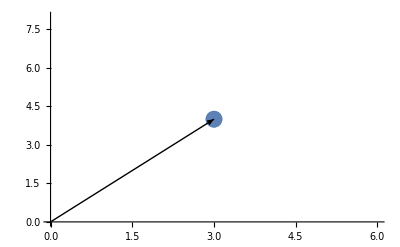

```mathematica
z0 = 3+4 I
z0coords = z0 // complexToXY
plot1=ListPlot[{z0coords},PlotStyle->PointSize[0.03]];
plot2 = Graphics[Arrow[{{0,0},z0coords}] ];
Show[plot1,plot2]
```

### a)

```mathematica
Re[z0]
Im[z0]
```

3

4

The real component can be thought of (inaccurately) as the x component of the complex plane and the imaginary part as the y component

### b)

```mathematica
Abs[z0]
Arg[z0]*180/π//N
```

5

53.1301

The “Abs” represents the magnitude of the vector formed, or the length of the arrow. The “Arg” represents the angle made between x= 0 and the arrow.

### c)

3-4 ⅈ

{3,-4}

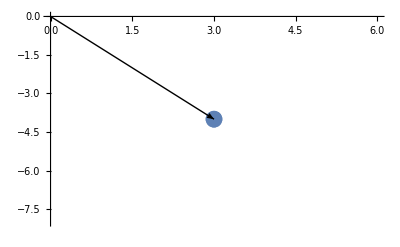

```mathematica
z01 = Conjugate[z0]
z01coords = z01 // complexToXY
plot11=ListPlot[{z01coords},PlotStyle->PointSize[0.03]];
plot22 = Graphics[Arrow[{{0,0},z01coords}] ];
Show[plot11,plot22]
```

We can think of the complex conjugate as the reflection across the ‘real’ axis.

## Assignment 2 ✓

### a)

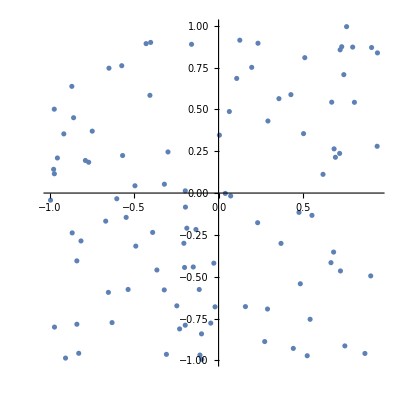

```mathematica
complist2 =RandomComplex[{-1-I, 1+I}, 100];
complist2M = Map[complexToXY, complist2];
ListPlot[complist2M, AspectRatio->1]
```

### b)

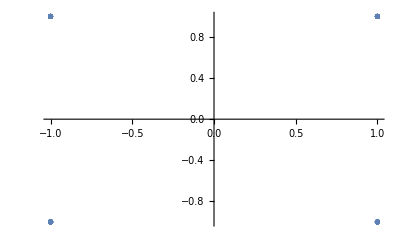

```mathematica
ListPlot[Map[Sign, complist2M]]
```

It looks like Sign gives the -1 or 1 (negative or positive) values of each term in the list. So -.094 + 0.4i would be {-1,1}.

## Assignment 3 ✓

### a)

```mathematica
ExpToTrig[E^(I*x)]
```

Cos[x]+ⅈ Sin[x]

Yep it knows the formula.

### b)

```mathematica
ExpToTrig[E^x]
```

Cosh[x]+Sinh[x]

### c)

```mathematica
TrigToExp[{Cos[x], Sin[x]}]
```

{ⅇ^(-ⅈ x)/2+ⅇ^(ⅈ x)/2,1/2 ⅈ ⅇ^(-ⅈ x)-1/2 ⅈ ⅇ^(ⅈ x)}

### d)

```mathematica
TrigToExp[{Cosh[x], Sinh[x]}]
```

{ⅇ^-x/2+ⅇ^x/2,-ⅇ^-x/2+ⅇ^x/2}

### e)

I’m glad that all these results are used so frequently in physics classes that they are worth memorizing. I will do so.

## Assignment 4 ✓

1.06473+1.9663 ⅈ

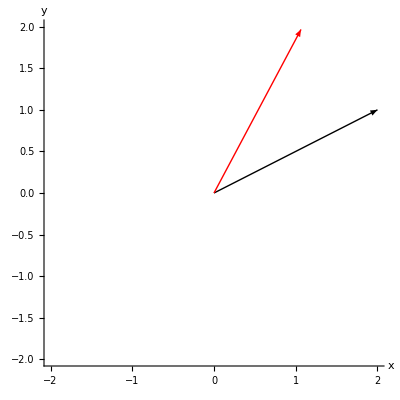

35.

```mathematica
Clear[z2]
rotate[number_, angle_] := E^(I*angle)(Abs[number] E^(Arg[number]*I))
z2 = 2 + I;
z2rot = rotate[z2, 35*π/180] //N
objects4:= { Arrow[{{0,0},complexToXY[z2]}] , Red, Arrow[{{0,0},complexToXY[z2rot]}] };
Graphics[objects4, PlotRange->{{-2,2}, {-2,2}}, AspectRatio->1, Axes->True, AxesLabel->{"x","y"}]
(*to check*)
180/π(Arg[z2rot] - Arg[z2]) 
(*ok i think it's good.*)
```

## Assignment 5 ✓

An exploration of Snell’s law.

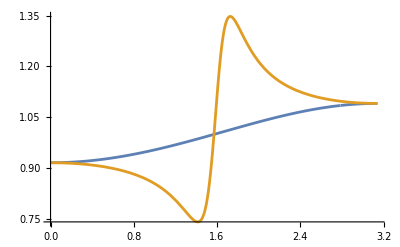

```mathematica
λ5 = 532*^-9;
Subscript[n, Al] = 0.939+6.42I;
Subscript[n, Air] = 1;
P = 0.001 (*W*);
(*n1 = air, n2 = al*)
Subscript[θ, t] = ArcSin[(Subscript[n, Air] Sin[θ])/Subscript[n, Al]];

Subscript[R, s][θ_] = Abs[(Subscript[n, Air] Cos[θ] - Subscript[n, Al] Cos[Subscript[θ, t]])/(Subscript[n, Air] Cos[θ] + Subscript[n, Al] Cos[Subscript[θ, t]])]^2;
Subscript[R, p][θ_] = Abs[(Subscript[n, Air] Cos[Subscript[θ, t]] - Subscript[n, Al] Cos[θ])/(Subscript[n, Air] Cos[Subscript[θ, t]] + Subscript[n, Al] Cos[θ])]^2;

Plot[{Subscript[R, s][θ], Subscript[R, p][θ]}, {θ, 0π, π},PlotRange->All]
```

### b)

```mathematica
θB = ArcTan[Subscript[n, Al]/Subscript[n, Air]]
angle = FindMinimum[Subscript[R, p][θ], {θ, 1.4}][[2]]//Quiet
θ*180/π/.angle
Subscript[R, p][θ]/.angle
```

1.54796+0.15362 ⅈ

{θ→1.4145}

81.0448

0.742261

Reflected angle = 81 degree, P = 0.742 Units

## Assignment 6 ✓

### a)

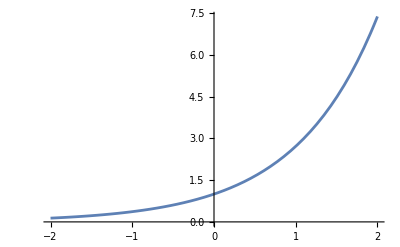

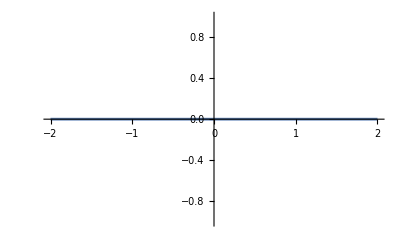

```mathematica
(*Plot3D, function of x and y where x is real and y is imaginary*)
(*Re = Cosθ, Im = Sinθ*)



Plot[Re[E^x], {x,-2,2}]
Plot[Im[E^y], {y, -2,2}]
```

### b)

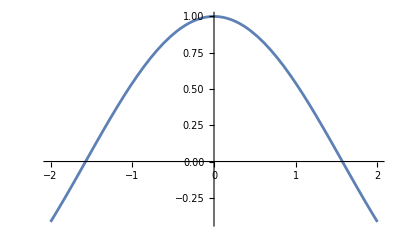

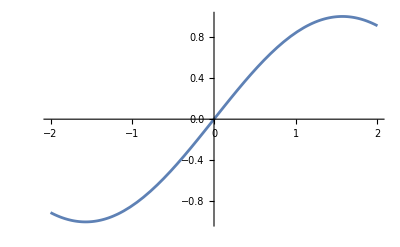

```mathematica
Plot[Re[E^(I*x)],{x,-2,2}]
Plot[Im[E^(I*y)], {y,-2,2}]
```

### c)

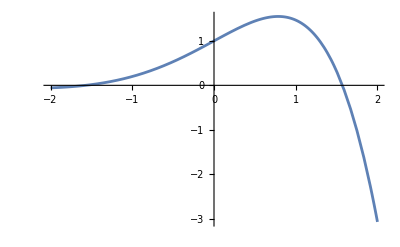

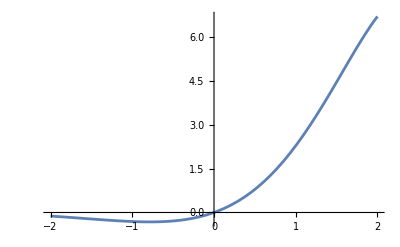

```mathematica
Plot[Re[E^(x+I*x)], {x,-2,2}]
Plot[Im[E^(y+I*y)], {y, -2,2}]
```

### d)

```mathematica
(*real*)
Plot3D[Re[Cos[x+ I*y]+I*Sin[x+I y]], {x,-2,2}, {y,-2,2}, PlotRange->All, Mesh->None, ColorFunction->"PearlColors", ViewPoint->{-2, 0, 0}]

Plot3D[Re[Cos[x+ I*y]+I*Sin[x+I y]], {x,-2,2}, {y,-2,2}, PlotRange->All, Mesh->None, ColorFunction->"PearlColors", ViewPoint->{0,-2,0}]

Plot3D[Re[Cos[x+ I*y]+I*Sin[x+I y]], {x,-2,2}, {y,-2,2}, PlotRange->All, Mesh->None, ColorFunction->"PearlColors", ViewPoint->{-2,-2,0}]

(*Imaginary*)

Plot3D[Im[Cos[x+I*y]+I*Sin[x+I y]], {x,-2,2}, {y,-2,2}, PlotRange->All, Mesh->None, ColorFunction->"AuroraColors", ViewPoint->{Front}]

Plot3D[Im[Cos[x+I*y]+I*Sin[x+I y]], {x,-2,2}, {y,-2,2}, PlotRange->All, Mesh->None, ColorFunction->"AuroraColors", ViewPoint->{1.3, -2.4, 2.}]


Plot3D[Im[Cos[x+I*y]+I*Sin[x+I y]], {x,-2,2}, {y,-2,2}, PlotRange->All, Mesh->None, ColorFunction->"AuroraColors", ViewPoint->{2,2,0}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»

### e)

```mathematica
ComplexExpand[E^(x + I*y)]
```

ⅇ^x Cos[y]+ⅈ ⅇ^x Sin[y]

You can see the cosine and sine components, evident from the different displays of the 3d Plot. They are in order.

## Assignment 7 ✓

### a) ✓

```mathematica
f=1/(1-Exp[z - 0.5]) 
list={Re[f],Im[f]}   /. z-> x+I y
Plot3D[# , {x,-2 , 2 },{y,-2 ,2 },AxesLabel->{"x","y",None},PlotRange->{-10,10}, PlotLabel->#]&  /@ list
```

1/(1-ⅇ^(-0.5+z))

{Re[1/(1-ⅇ^(-0.5+x+ⅈ y))],Im[1/(1-ⅇ^(-0.5+x+ⅈ y))]}

{-Graphics3D-,-Graphics3D-}

The pole appears at x = 0.5, y = 0

### b) ✓

```mathematica
Clear[z, z0]
series = Series[1/(1-Exp[z - 0.5]) ,{z,(0.5+ 0I),10}]   //Chop(*or z0?*)
 (* the series, evaluated at a point close to z = 2i *)
```

-1/(z-0.5)+1/2-(z-0.5)/12+1/720 (z-0.5)^3-(z-0.5)^5/30240+(z-0.5)^7/1209600-(z-0.5)^9/47900160+O[z-0.5]^11

#### c) ✓

```mathematica
SeriesCoefficient[series , -1]
SeriesCoefficient[series, 9]
```

-1

-1/47900160

#### d) ✓

```mathematica
Residue[1/(1-Exp[z - 0.5]),{z, (0.5- 0*I)} ]
```

-1.

## Assignment 8 ✓

```mathematica
pathintegral[f_,xoft_,yoft_,t_,tstart_,tend_] :=  Module[{extrafactor,foft},   
	(*  f = f(x,y);  
		xoft = x as func of t for the particular path, 
		yoft = y as func of t for the particular path,  
		t is just the letter t, 
		tstart and tend are limits of t  *)
extrafactor=Sqrt[D[xoft,t]^2 + D[yoft,t]^2];
foft = f /. {x->xoft, y-> yoft} ;
NIntegrate[foft * extrafactor,{t,tstart,tend}]
]
```

### a)

```mathematica
plot81=ParametricPlot3D[{x,y,x^2+ y^2} /.{ x -> Sqrt[t], y-> Sin[t*5 π/2]},{t,0,1}, BoxRatios->{1,1,1}]
```

-Graphics3D-

### b)

```mathematica
plot82 =ParametricPlot3D[{x,y,z}  /.{ x -> Sqrt[t], y-> Sin[t*5 π/2]},{t,0,1},{z,0 ,x^2+y^2/.{x->Sqrt[t], y->Sin[5 π/2 t]}}, BoxRatios->{1,1,1}, PlotPoints->100]
f = x ^2 + y^2;
plot1 = Plot3D[f,{x,-1.5,1.5},{y,-1.5,1.5} ,BoxRatios->{1,1,1}, Mesh->None, ColorFunction->"WatermelonColors"];
Show[plot1, plot82]
```

-Graphics3D-

-Graphics3D-

### c)

```mathematica
pathintegral[x^2 +y^2, Sqrt[t], Sin[t*(5π)/2],t,0,1] //N
```

4.27486

## Assignment 9

Exploration of Residuals.

```mathematica
g[z_] = 3/(z+z^3)
gplot=Plot3D[Abs[g[x+I y]],{x,-3,3},{y,-3,3},AxesLabel->{"x","y",None},Axes->{True,True,False},MeshStyle->Gray,PlotPoints->20,PlotRange->{0,10},LabelStyle->Medium,ViewPoint->{0,0,20},SphericalRegion->True]
```

3/(z+z^3)

-Graphics3D-

### a)

```mathematica
Residue[g[z], {z,0}]
Residue[g[z], {z, I}]
Residue[g[z], {z,-I}]
```

3

-3/2

-3/2

### b)

```mathematica
z0 = 0;  r= 1/2;  (* z0 is the expansion point, r is the integration-path radius *)
parametricpath[th_] := {r*Cos[th]+Re[z0],r*Sin[th]+Im[z0], Abs[g[r*(Cos[th]+I Sin[th])+z0]]}
Show[ gplot,
Plot3D[Abs[g[x+I y]],{x,-3,3},{y,-3,3},AxesLabel->{"x","y",None},Axes->{True,True,False},MeshStyle->Gray,PlotPoints->20,PlotRange->{0,10},LabelStyle->Medium,ViewPoint->{0,0,20},SphericalRegion->True],
ParametricPlot3D[parametricpath[th],{th,0,2Pi},PlotStyle->{Thickness[0.01],Black}]
]
z1= z0 +  r*Exp[I θ];
integrand = g[z1] D[z1,θ];
Integrate[integrand ,{θ,0,2Pi}]

z2 = I+ r*Exp[I*θ];
integrand2 = g[z2]*D[z2,θ];
Integrate[integrand2, {θ, 0 ,2π}]

z3 = -I+r*Exp[I*θ];
integrand3 = g[z3]*D[z3,θ];
Integrate[integrand3, {θ, 0, 2π}]
```

-Graphics3D-

6 ⅈ π

-3 ⅈ π

-3 ⅈ π

#### c)

```mathematica
z4 = 0+r*Exp[I*θ];
integrand4 = g[z4]*D[z4,θ];
Integrate[integrand4, {θ, 0, 2π}]
(*test 2*)
z5 = 4+r*Exp[I*θ];
integrand5 = g[z5]*D[z5,θ];
Integrate[integrand5, {θ, 0, 2π}]
(*test 3*)
z6 = 3+r*Exp[I*θ];
integrand6 = g[z6]*D[z6,θ];
Integrate[integrand6, {θ, 0, 2π}]
```

6 ⅈ π

0

0

### d)

```mathematica
z7 = 0;  r7= 2;  (* z0 is the expansion point, r is the integration-path radius *)
parametricpath[th_] := {r7*Cos[th]+Re[z0],r7*Sin[th]+Im[z0], Abs[g[r7*(Cos[th]+I Sin[th])+z7]]}
Show[ gplot,
Plot3D[Abs[g[x+I y]],{x,-3,3},{y,-3,3},AxesLabel->{"x","y",None},Axes->{True,True,False},MeshStyle->Gray,PlotPoints->20,PlotRange->{0,10},LabelStyle->Medium,ViewPoint->{0,0,20},SphericalRegion->True],
ParametricPlot3D[parametricpath[th],{th,0,2Pi},PlotStyle->{Thickness[0.01],Black}]
]
z8= z7 +  r7*Exp[I θ];
integrand8 = g[z8] D[z8,θ];
Integrate[integrand8 ,{θ,0,2Pi}]
SumRes =(Residue[g[z], {z, 0}] + Residue[g[z], {z,I}] + Residue[g[z], {z, -I}])

Integrate[integrand8 ,{θ,0,2Pi}] == SumRes
```

-Graphics3D-

0

0

True